## National Power as Network Flow

### Helper Functions

#### CenteredMovingAverage

The window width n is assumed to be odd. Non-smoothed values at the extremes are left alone.

```mathematica
CenteredMovingAverage[list_,n_]:= With[{len=(n-1)/2},
Catenate[{Take[list,len],MovingAverage[list,n],Take[list,-len]}]
]
```

#### ElementwiseMax

Given two numeric lists, return the elementwise maximum.

```mathematica
ElementwiseMax[lists_]:=Map[Max,Transpose[lists]]
```

#### OneHotEncodeMax

Make the largest element a 1 and the rest 0s.

```mathematica
OneHotEncodeMax[x_]:=ReplacePart[Table[0.,Length[x]],PositionLargest[x]->1.]
```

#### PositionLargest

Gives the position of the first element that has the largest value in list. Output: list of integers.

```mathematica
PositionLargest=ResourceFunction["PositionLargest"];
```

#### RelativeError

Measures the percentage error between lists of expected and actual numbers.

Better to use EuclideanDistance.

```mathematica
RelativeError[e_,a_]:= N[Total[Abs[a-e]]/Total[e]]
```

#### ReplaceColumn

Replace a column in a matrix M with a given list. Output: matrix.

```mathematica
ReplaceColumn[M_List,i_Integer,list_List]:=Block[{m=M},
m[[All,i]]=list;
Return[m];
]
```

### Data Queries

#### File Path

```mathematica
path="/Users/mpoulshock/Documents/Github/AMathematicalTheoryOfPowerStruggles/Papers/4 - National Power as Network Flow/Data/";
```

#### Country Name and ID

```mathematica
countryData=Import[path<>"World Power Structure/Countries.csv","Data"];
```

```mathematica
countries = Map[#[[2]]&,Rest[countryData]];
```

```mathematica
CountryName[id_]:=countries[[id]]
```

```mathematica
CountryID[name_]:= First[FirstPosition[countries,name]]
```

#### Wealth (1995-2020)

```mathematica
wealthData=Import[path<>"World Power Structure/CountryYearsWealth.csv","Data"]
```

{{Year,Country,National Wealth},{1995,1,9.57×10^10},{1996,1,1.02×10^11},{1997,1,9.69×10^10},{1998,1,9.23×10^10},{1999,1,9.×10^10},{2000,1,8.33×10^10},{2001,1,7.69×10^10},5003,{2013,193,7.86×10^10},{2014,193,8.21×10^10},{2015,193,8.47×10^10},{2016,193,8.58×10^10},{2017,193,9.09×10^10},{2018,193,9.72×10^10},{2019,193,7.47×10^10},{2020,193,7.×10^10}}
 |  |  |  |

```mathematica
NationalWealth[countryID_,year_]:=Block[{r},
r=SelectFirst[wealthData,#[[1]]==year&&#[[2]]==countryID&];
If[r===Missing["NotFound"],0.,r[[3]]]
]
```

```mathematica
NationalWealth[193,1995]
```

1.2×10^11

```mathematica
WealthVector[year_]:= WealthVector[year]= Array[NationalWealth[#,year]&,193]
```

```mathematica
WealthVector[1996]
```

A list of all national wealth lists from 1995-2020.

```mathematica
WealthSeries = Map[WealthVector,Range[1995,2020]];
```

Extracts a time interval from the WealthSeries.

```mathematica
WealthSeriesInterval[start_,end_]:=Take[WealthSeries,{start-1994,end-1994}]
```

Get the wealth series for a given country, over the entire 25-year interval.

```mathematica
CountryWealthSeries[cid_Integer]:=WealthSeries[[All,cid]];
CountryWealthSeries[name_String]:=CountryWealthSeries[CountryID[name]];
```

A list of the largest countries in a given year.

```mathematica
LargestNCountries[n_,year_]:=Take[Reverse[Ordering[WealthVector[year]]],n]
```

```mathematica
LargestNCountries[10,2020]
```

{37,186,78,86,65,162,61,170,79,185}

WealthSeries with a 3-period moving average applied to each country vector.

```mathematica
SmoothedWealthSeries=Transpose[Map[CenteredMovingAverage[#,3]&,Transpose[WealthSeries]]];
```

#### DOTS Merchandise Trade (1995-2020)

Import the DOTS data set.

```mathematica
dotsData=Import[path<>"Edited/IMF DOTS Subset.csv","Data"];
```

For a given year, convert the dyadic data to a list of rules.

```mathematica
dotsYearRules[year_]:=Map[{#[[1]],#[[2]]}->N[#[[year-1992]]]&,Rest[dotsData]]
```

```mathematica
dotsYearRules[2020]
```

{{6,179}→1.96182×10^8,{6,108}→815000.,{6,140}→7.8516×10^7,{6,158}→1.8056×10^7,{6,137}→1.17519×10^8,{6,152}→3000.,{6,16}→6.623×10^6,{6,155}→7000.,{6,85}→5.684×10^6,33528,{191,181}→0.,{193,56}→2135.,{192,189}→29.,{191,91}→0.,{192,174}→0.,{192,132}→0.,{191,24}→0.,{191,135}→0.,{191,145}→1094.}
 |  |  |  |

Generate the goods trade matrix for a given year.

```mathematica
G[year_]:= G[year]=ReplacePart[ConstantArray[0.,{193,193}],dotsYearRules[year]]
```

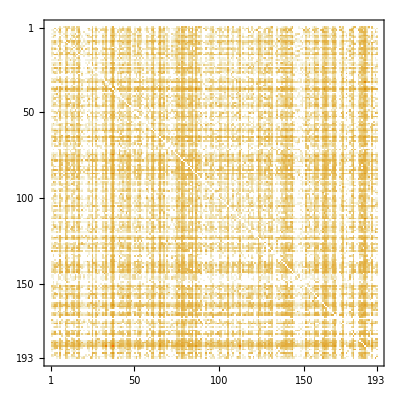

```mathematica
G[2020]//MatrixPlot
```

#### BATIS Services Trade (1995-2012)

Import the BATIS data set.

```mathematica
batisData=Import[path<>"Edited/OECD-WTO BATIS Data 1995-2012.csv","Data"]
```

{{Year,Exporter,Importer,S200CurrentUSDMillion},{2008,91,184,14.2289},{2008,91,1,0.6013},{2008,91,5,0.059},{2008,91,2,7.9552},{2008,91,7,0.7588},{2008,91,4,10.2353},580339,{2012,193,155,0.0762},{2012,193,169,0.019},{2012,193,175,0.0151},{2012,193,178,0.156},{2012,193,177,2.5447},{2012,193,187,0.0117},{2012,193,188,0.374}}
 |  |  |  |

Segment the data by year.

```mathematica
batisDataByYear[year_]:=batisDataByYear[year]=Select[batisData,#[[1]]==year&]
```

For a given year, convert the dyadic data to a list of rules.

```mathematica
batisYearRules[year_]:=Map[{#[[2]],#[[3]]}->N[#[[4]]]&,batisDataByYear[year]]
```

Generate the BATIS matrix.

```mathematica
batisYear[year_]:= batisYear[year]=ReplacePart[ConstantArray[0.,{193,193}],batisYearRules[year]]
```

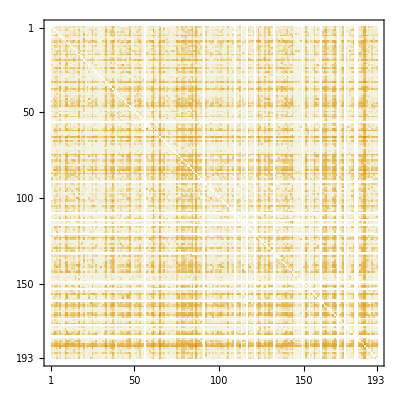

```mathematica
batisYear[1995]//MatrixPlot
```

#### WTO Services Trade (2013-2020)

Import the WTO services trade data.

```mathematica
wtoData=Import[path<>"Edited/WTO Services Exports 2013-2020 (processed).csv","Data"]
```

{{Exporter,Importer,2013,2014,2015,2016,2017,2018,2019,2020},{2,1,0,0,0,0,0,0,0,0},{10,1,1,1,2,2,2,2,1,0},{17,1,8,9,4,3,2,6,7,0},{23,1,0,0,0,0,0,0,0,0},{27,1,1,1,1,1,1,1,1,0},6469,{143,193,0,0,0,0,0,0,0,0},{153,193,0,0,0,0,0,0,0,0},{157,193,0,0,0,0,0,0,0,0},{158,193,0,0,0,0,0,0,0,0},{167,193,25,29,18,15,8,2,7,0},{185,193,103,146,84,0,0,0,0,0}}
 |  |  |  |

For a given year, convert the dyadic data to a list of rules.

```mathematica
wtoYearRules[year_]:=Map[{#[[1]],#[[2]]}->N[#[[year-2010]]]&,Rest[wtoData]]
```

Generate the trade matrix for a given year.

```mathematica
wtoYear[year_]:= wtoYear[year]=ReplacePart[ConstantArray[0.,{193,193}],wtoYearRules[year]]
```

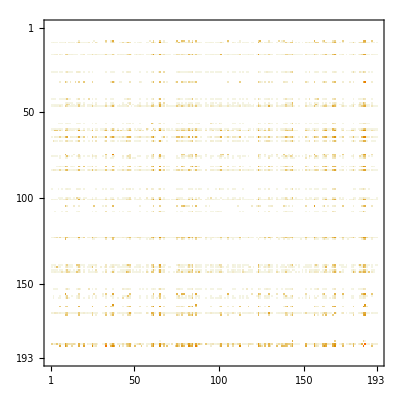
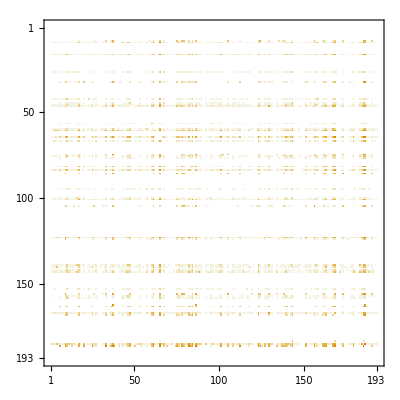
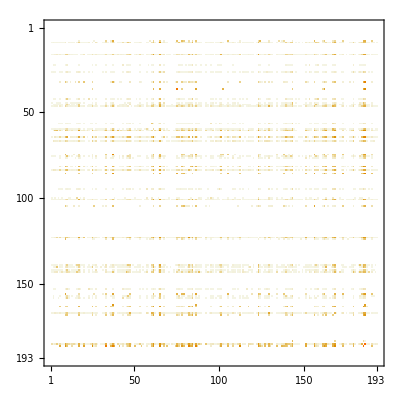
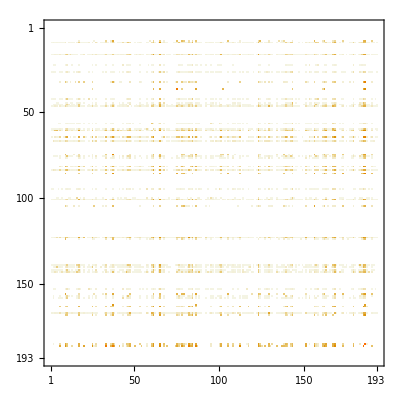
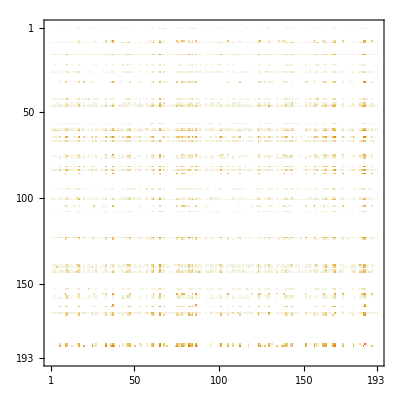
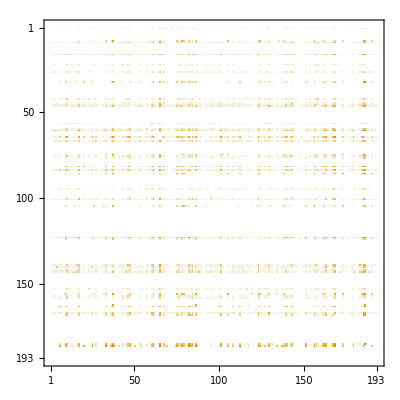
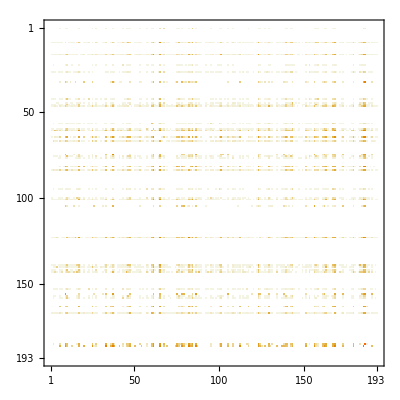
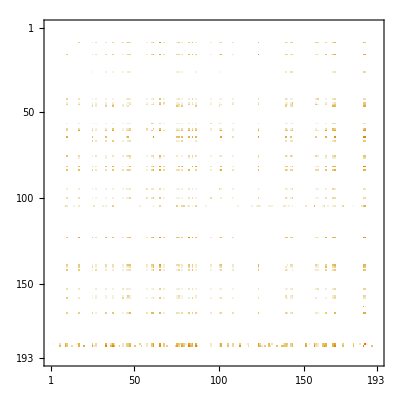
{-Graphics-
2013,-Graphics-
2014,-Graphics-
2015,-Graphics-
2016,-Graphics-
2017,-Graphics-
2018,-Graphics-
2019,-Graphics-
2020}

```mathematica
Map[Column[{MatrixPlot[wtoYear[#]],#}]&,Range[2013,2020]]
```

#### Services Trade (1995-2020)

Select the appropriate dataset and multiply by 1000000 to get the result in current USD.

```mathematica
S[year_]:=If[year≥ 2013,wtoYear[year],batisYear[year]]*1000000.
```

#### Major Interstate Conflicts (1995-2020)

```mathematica
conflicts = Import[path<>"Edited/Interstate Wars 1995-2020 - DyadYears.csv","Data"];
```

For Syria counterfactual (no civil war)

```mathematica
conflicts = Import[path<>"Edited/Interstate Wars 1995-2020 - DyadYears (Syria counterfactual).csv","Data"];
```

```mathematica
conflictsInYear[year_]:= Select[conflicts,#[[4]]==year&]
```

```mathematica
conflictYear[year_]:=ReplacePart[ConstantArray[0.,{193,193}],Map[{#[[6]],#[[5]]}->#[[7]]&,conflictsInYear[year]]]
```

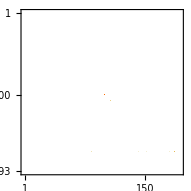

```mathematica
conflictYear[2014]//MatrixPlot
```

Matrix of dyadic conflict expenditures.

```mathematica
ConflictMatrix[year_]:=conflictYear[year]*1000000.*conversionFactorToUSD2020[year]
```

Estimated expenditure (in USD 2020) by each country in a given year.

```mathematica
ConflictVector[year_]:=Total[ConflictMatrix[year]]
```

#### Currency conversion

```mathematica
conversionData=Import[path<>"Original/CurrencyConversions.csv","Data"]
```

{{Year,Conversion Factor to USD 2020},{1995,1.6982},{1996,1.6495},{1997,1.6125},{1998,1.5878},{1999,1.5535},{2000,1.503},{2001,1.4614},{2002,1.4386},{2003,1.4066},{2004,1.3701},{2005,1.3252},{2006,1.2838},{2007,1.2482},{2008,1.2021},{2009,1.2064},{2010,1.1869},{2011,1.1506},{2012,1.1273},{2013,1.111},{2014,1.0933},{2015,1.092},{2016,1.0784},{2017,1.0559},{2018,1.0302},{2019,1.0123},{2020,1}}

```mathematica
conversionFactorToUSD2020[year_]:=N[SelectFirst[conversionData,#[[1]]==year&][[2]]]
```

```mathematica
conversionFactorToUSD2020[2008]
```

1.2021

#### Trade Matrix and Vector

Returns a matrix indicating bilateral trade volumes in USD 2020.

```mathematica
TradeMatrix[year_]:=TradeMatrix[year]=(G[year]+Transpose[G[year]]+S[year]+Transpose[S[year]])*conversionFactorToUSD2020[year]
```

Returns a vector representing each country’s total trade volume (imports and exports of goods and services) in USD 2020.

```mathematica
TradeVector[year_]:=Total[TradeMatrix[year]]
```

A time series (1995-2020) of the trade volume of a given country

```mathematica
CountryTradeSeries[country_]:=Map[Total[TradeMatrix[#][[CountryID[country]]]]&,Range[1995,2020]]
```

#### Democracy Index

Democracy Index scores for 2020, as determined by the Economist Intelligence Unit and reported in Wikipedia: https://en.wikipedia.org/wiki/Democracy_Index#By_country. Higher numbers indicate that countries are more democratic; lower numbers indicate that they’re more autocratic. “Full democracies” have a score of 8 or more; “flawed democracies” 6 or more; “hybrid regimes” 4 or more; and “authoritarian” regimes scores less than 4.

```mathematica
democracyData=Import[path<>"Original/Democracy Index (EIU) (2020).csv","Data"];
```

This data does not include all 193 countries.

```mathematica
Length[democracyData]
```

164

Initial coalitions (red and blue). We’ll add to these one state at a time, based on which coalition each state has more trade with. “Full democracies” have a score of 8 or more; “flawed democracies” 6 or more; “hybrid regimes” 4 or more; and “authoritarian” regimes scores less than 4. U.S. Democracy Index = 7.92; China = 2.27.

```mathematica
reds=Map[CountryID[#[[2]]]&,Select[democracyData,First[#]<2.4&]];
blues=Map[CountryID[#[[2]]]&,Select[democracyData,First[#]>7.9&]];
```

#### SIPRI Military Expenditure Data (1949-2020)

```mathematica
milexData=Import[path<>"Original/SIPRI Milex Data (Polarity).csv","Data"];
```

#### Data gaps

Venezuela was omitted because the national wealth figures were implausibly high.

Taiwan doesn’t have any trade data.

```mathematica
Tpos[2020][[170]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### Tactic Matrix

#### NormalizeT

Normalize a component of the tactic matrix by scaling it to the size (wealth) vector.

```mathematica
NormalizeT[s_,T_]:=N[Transpose[Transpose[T]/s]]
```

Generate the vector to be used for normalizing components of the tactic matrix. This vector is the elementwise maximum of the wealth vector (from the prior year) and the expenditure vector.

```mathematica
NormalizationVector[year_]:=ElementwiseMax[{WealthVector[year-1],ExpenditureVector[year]}]
```

Total power expended (vector)

```mathematica
ExpenditureVector[year_]:=Total[TradeMatrix[year]+ConflictMatrix[year]]
```

Undo the normalization of a tactic matrix.

```mathematica
DenormalizeT[s_,T_]:=N[Transpose[Transpose[T]*s]]
```

#### Tpos

For each year, a T+ matrix is assembled from the goods (G) and services (S) trade data: T = G + Transpose[G] + S + Transpose[S]. Then need to convert the result to USD 2020. The resulting matrix reflects the percentage of national wealth allocated towards dyadic trade. It is not symmetric due to the normalization step.

```mathematica
Tpos[year_]:=Tpos[year]=NormalizeT[NormalizationVector[year],TradeMatrix[year]]
```

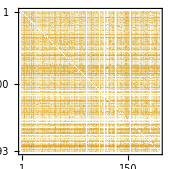

```mathematica
Tpos[1999]//MatrixPlot
```

#### Tneg

Construct the conflict matrix for a given year by importing the conflict data and converting it to USD 2020.

```mathematica
Tneg[year_]:=Tneg[year]=NormalizeT[NormalizationVector[year],ConflictMatrix[year]]
```

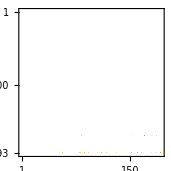

```mathematica
Tneg[2015]//MatrixPlot
```

#### Tzed

```mathematica
Tzed[year_]:= DiagonalMatrix[1.-Total[Tpos[year]]-Total[Tneg[year]]]
```

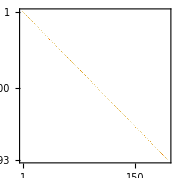

```mathematica
Tzed[2009]//MatrixPlot
```

### Parameters

#### General

The parameters β and λ are assumed to be scalars in this implementation.

```mathematica
μ=30;
λ=1.025;
β =1.392;
```

#### Relationship between trade and growth

What is the relationship between one year’s trade volume and the next year’s growth (in wealth)? Want to plot growth % as a function of  trade % and see what the distribution of points looks like.

1.02532+0.201237 tradePercentage

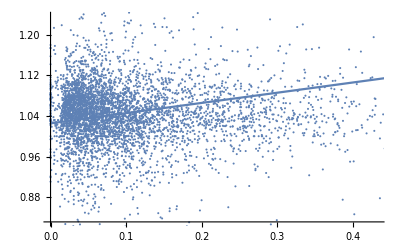

```mathematica
growthPct=WealthSeriesInterval[1996,2020]/WealthSeriesInterval[1995,2019];
tradePct=Map[TradeVector[#]/WealthVector[#-1]&,Range[1996,2020]];
data=Thread[{Flatten[tradePct],Flatten[growthPct]}];
eq=Fit[data,{1,tradePercentage},tradePercentage]
Show[ListPlot[data],Plot[eq,{tradePercentage,0,1}]]
```

The linear equation above suggests that on average national wealth increases annually by 2.5% due to factors unrelated to trade and at a rate of 4.0% due to trade.

```mathematica
0.201237*Mean[Flatten[tradePct]]
```

0.0398262

The average annual growth in wealth is 6.5% (≈2.5+4.0%).

```mathematica
Mean[Flatten[growthPct]]
```

1.06515

Trade/growth ratio ≈ 2

```mathematica
growth=WealthSeriesInterval[1996,2020]-WealthSeriesInterval[1995,2019];
trade=Map[TradeVector[#]&,Range[1996,2020]];
Quiet[Mean[Select[Flatten[trade]/Flatten[growth],#≠ComplexInfinity&]]]
```

1.98847

#### Estimating β (scalar)

Finding parameters that minimize the average error (Euclidean distance) between the actual and predicted wealth vectors, for each year from 1996-2020. Assuming β is a scalar and λ = 1.0253. This is a sliding simulation. With this method, β = 1.392. This is the more sound method to use, because SimulateDynamicT depends upon an ongoing time series that gets increasingly inaccurate.

```mathematica
error[beta_]:=Block[{},
μ=30;
λ=1.0253;
β =beta;
Mean[MapThread[EuclideanDistance,{Map[UpdateS,Range[1996,2020]],Rest[WealthSeries]}]]
]
```

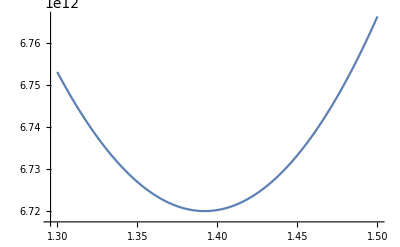

```mathematica
results=Map[{#,error[#]}&,Range[1.3,1.5,.001]];
ListLinePlot[results]
```

```mathematica
Take[Sort[Map[Reverse,results]],10]
```

{{6.72×10^12,1.392},{6.72×10^12,1.393},{6.72×10^12,1.391},{6.72001×10^12,1.394},{6.72002×10^12,1.39},{6.72003×10^12,1.395},{6.72004×10^12,1.389},{6.72006×10^12,1.396},{6.72006×10^12,1.388},{6.72009×10^12,1.397}}

Same as above, but using SimulateDynamicT instead of UpdateS[year]. With this method, β = 1.332.

```mathematica
error[beta_]:=Block[{sim,actual},
μ=30;
λ=1.0253;
β =beta;
sim=SimulateDynamicT[1996,2020];
actual=Rest[WealthSeries];
Mean[MapThread[EuclideanDistance,{sim,actual}]]
]
```

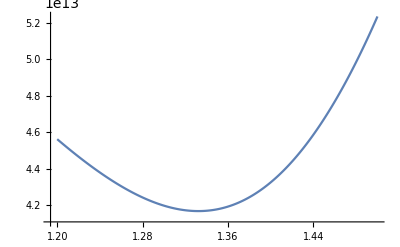

```mathematica
results=Map[{#,error[#]}&,Range[1.2,1.5,.001]];
ListLinePlot[results]
```

```mathematica
Take[Sort[Map[Reverse,results]],10]
```

{{4.16925×10^13,1.332},{4.16926×10^13,1.333},{4.16929×10^13,1.331},{4.16933×10^13,1.334},{4.1694×10^13,1.33},{4.16947×10^13,1.335},{4.16957×10^13,1.329},{4.16967×10^13,1.336},{4.1698×10^13,1.328},{4.16993×10^13,1.337}}

### Law of Motion

#### UpdateS

Apply the law of motion to a size vector and components of a tactic matrix. These functions can accept β and λ as either scalars or vectors. Output: size vector.

```mathematica
UpdateS[s_,Tpos_,Tneg_,Tzed_]:= Ramp[(β Tpos-μ Tneg+λ Tzed).s]
```

Apply the law of motion to a given year. Note that this uses the wealth vector of the prior year, based on the assumption that national wealth is measured on the last day of the calendar year (and thus it is the prior year’s wealth vector that is altered by the current year’s trade and military activity). So this function will return the projected national wealth as of the last day of the year, enabling a direct comparison between UpdateS[year] and WealthVector[year]. Output: size vector.

```mathematica
UpdateS[year_]:=UpdateS[WealthVector[year-1],year]
```

Apply the law of motion, given a tactic matrix for a specific year, as well as  a size vector. Output: size vector.

```mathematica
UpdateS[s_,year_]:=UpdateS[s,Tpos[year],Tneg[year],Tzed[year]]
```

#### Simulate

Simulate the law of motion over several steps. Output: list of size vectors.

```mathematica
Simulate[year_,n_]:=NestList[UpdateS[#,year]&,WealthVector[year-1],n]
```

Simulate the law of motion over a given  time period, where s_0 is the initial size vector and where T varies every year. Output: list of size vectors.

```mathematica
SimulateDynamicT[start_,end_]:=FoldList[UpdateS,WealthVector[start],Range[start+1,end]];
```

Extract simulation data for selected countries (by country ID). Output: list of size vectors.

```mathematica
SimulationSubset[sim_,countryIDs_List]:=Map[#[[countryIDs]]&,sim]
```

#### SizeSeriesSubsetPlot

Given a time series of wealth vectors from all countries, extract specified countries and plot them.

```mathematica
SizeSeriesSubsetPlot[sim_,countryIDs_,startYear_,title_]:=ListLinePlot[Map[Transpose[{Range[startYear,startYear+Length[sim]-1],#}]&,Transpose[SimulationSubset[sim,countryIDs]]],PlotLabels->Map[CountryName,countryIDs],AxesLabel->{"Year","USD 2020"},PlotLabel->title,PlotRange->All]
```

```mathematica
SizeSeriesSubsetPlot[SmoothedWealthSeries,RandomChoice[Range[193],10],1995,"Rando"]
```

-Graphics-

#### SlidingSimulation

Projects a country’s wealth in a given year, based on the prior year’s data. (These functions are not used in the paper.)

```mathematica
WealthProjection[countryName_,year_]:=Block[{},
λ=1.025;
β=1.395;
UpdateS[year][[CountryID[countryName]]]
]
```

Projects a country’s wealth in a series covering several years, where each year uses data from the prior year.

```mathematica
SlidingSimulation[countryName_,startYear_,endYear_]:= Map[WealthProjection[countryName,#]&,Range[startYear,endYear]]
```

```mathematica
SlidingSimulation["Afghanistan",2000,2002,3]
```

{8.70524×10^10,6.82186×10^10,8.01755×10^10}

#### Comparison Plots

Base function that generates the comparison plot.

```mathematica
ComparisonPlot[sim_,actual_,countryName_,startYear_,endYear_]:= Block[{}, 
ListLinePlot[Map[Transpose[{Range[startYear,startYear+Length[sim]-1],#}]&,{sim,actual}],PlotLabels->{"Model","Actual"},AxesLabel->{"Year","USD 2020"},PlotLabel->countryName<>" ("<>ToString[startYear]<>"-"<>ToString[endYear]<>")",PlotRange->All,Ticks->Range[startYear,endYear]]
]
```

Generates a wealth series plot that compares the actual national wealth of a given country with the wealth predicted by a sliding simulation. (This function is not used in the paper.)

```mathematica
ComparisonPlotSliding[countryName_,startYear_,endYear_]:= Block[{sim,actual},
sim=SlidingSimulation[countryName,startYear,endYear];
actual=Transpose[WealthSeriesInterval[startYear,endYear]][[CountryID[countryName]]]; 
ComparisonPlot[sim,actual,countryName,startYear,endYear]
]
```

```mathematica
ComparisonPlotSliding[RandomChoice[countries],1999,2018]
```

-Graphics-

```mathematica
ComparisonPlotSliding["United States",1999,2020]
```

-Graphics-

Compares the actual wealth series to the model, assuming that the initial size vector is iteratively updated based on a tactic matrix that varies every year.

```mathematica
ComparisonPlotDynamicT[countryName_,start_,end_]:= Block[{sim,actual,c=CountryID[countryName]},
sim=SimulateDynamicT[start,end][[All,c]];
actual=Transpose[WealthSeriesInterval[start,end]][[c]]; 
ComparisonPlot[sim,actual,countryName,start,end]
]
```

```mathematica
ComparisonPlotDynamicT["United States",2010,2018]
```

-Graphics-

Compares the actual wealth series to the model, assuming that the initial size vector and tactic matrix are held constant.

```mathematica
ComparisonPlotNaive[countryName_,start_,end_]:= Block[{sim,actual,c=CountryID[countryName]},
sim=Simulate[start,end-start][[All,c]];
actual=Transpose[WealthSeriesInterval[start,end]][[c]]; 
ComparisonPlot[sim,actual,countryName,start,end]
]
```

```mathematica
ComparisonPlotNaive["United States",2002,2010]
```

-Graphics-

#### ReallocateTrade

Reallocate a percentage of a state’s power (trade volume) away from its opponents and towards its allies. The input matrix is assumed to be a trade matrix. Output: trade matrix.

```mathematica
ReallocateTrade[i_Integer,T_,allies_List,opponents_List,pct_]:=Block[{len=Length[T],dT=T,reducedT,diff,add,addT},
(* Reduce i's trade with opponents by pct *)
reducedT=ReplacePart[dT,Flatten[Map[{{#,i}->dT[[#,i]]*(1.-pct),{i,#}->dT[[i,#]]*(1.-pct)}&,opponents]]];

(* Total amount of trade reduction with opponents *)
diff=Total[Map[dT[[i,#]]*pct&,opponents]];

(* Reallocation of that trade to allies *)
add=allocationPct[ReplacePart[ConstantArray[0.,len],Map[#-> dT[[#,i]]&,allies]]]*diff;
addT=ReplacePart[ReplaceColumn[ConstantArray[0.,{len,len}],i,add],{i->add}];

reducedT+addT
]
```

A version that references global variables, used in a Fold, e.g. Fold[ReallocateTrade,T,allies].

```mathematica
ReallocateTrade[T_,i_]:=ReallocateTrade[i,T,allies,opps,pct]
```

Normalize the vector of trade allocated to an country’s allies, such that the vector total equals 1.

```mathematica
allocationPct[s_]:=If[Total[s]==0.,s,s/Total[s]]
```

#### Naive Simulation

```mathematica
year=2009;
μ=20;
λ=1.025;
β =1.395;
n=6;
timespan=10;
sim=Simulate[year,timespan];
top=Map[Take[ReverseSort[Transpose[{#,countries}]],n]&,sim];
topN=Map[CountryID,DeleteDuplicates[Map[#[[2]]&,Flatten[top,1]]]];
SizeSeriesSubsetPlot[sim,topN,year,"Predicted Wealth ("<>ToString[year]<>"-"<>ToString[year+timespan]<>")"]
```

-Graphics-

### Figures

#### Largest Countries by National Wealth (1995-2020)

A combined list of the biggest N countries in each year from 1995-2020.

```mathematica
SizeSeriesSubsetPlot[WealthSeries,Map[CountryID,{"China","United States","India", "Japan","Germany","South Korea", "France", "Russia"}],1995,""]
```

-Graphics-

#### Basic Comparison Plots

```mathematica
ComparisonPlotDynamicT["Azerbaijan",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Canada",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Cote d'Ivoire",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Nauru",1996,2020]
```

-Graphics-

#### Conflict Comparison Plots

```mathematica
ComparisonPlotDynamicT["Syrian Arab Republic",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Yemen",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Libya",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Iraq",1996,2020]
```

-Graphics-

```mathematica
ComparisonPlotDynamicT["Afghanistan",1999,2003]
```

-Graphics-

#### Syria Counterfactual

Actual wealth series (Syria)

```mathematica
Transpose[WealthSeriesInterval[1996,2020]][[CountryID["Syrian Arab Republic"]]]
```

{5.26×10^11,5.38×10^11,5.89×10^11,5.69×10^11,5.85×10^11,6.35×10^11,6.81×10^11,6.98×10^11,7.7×10^11,8.4×10^11,9.07×10^11,9.79×10^11,1.03×10^12,1.1×10^12,1.13×10^12,1.2×10^12,8.86×10^11,6.64×10^11,5.72×10^11,5.44×10^11,5.3×10^11,5.25×10^11,5.37×10^11,5.5×10^11,5.8×10^11}

```mathematica
actual={5.26*^11,5.38*^11,5.89*^11,5.69*^11,5.85*^11,6.35*^11,6.81*^11,6.98*^11,7.7*^11,8.4*^11,9.07*^11,9.79*^11,1.03*^12,1.1*^12,1.13*^12,1.2*^12,8.86*^11,6.64*^11,5.72*^11,5.44*^11,5.3*^11,5.25*^11,5.37*^11,5.5*^11,5.8*^11};
```

Counterfactual prediction, assuming no civil war. Note, this requires modifying the Interstate Wars 1995-2020 - DyadYears.csv file.

```mathematica
SimulateDynamicT[1996,2020][[All,CountryID["Syrian Arab Republic"]]]
```

{5.26×10^11,5.4415×10^11,5.62498×10^11,5.82591×10^11,6.11421×10^11,6.42372×10^11,6.76514×10^11,7.12326×10^11,7.47772×10^11,7.76964×10^11,8.09642×10^11,8.63271×10^11,9.202×10^11,9.71627×10^11,1.04911×10^12,1.09905×10^12,1.13993×10^12,1.17001×10^12,1.1977×10^12,1.22563×10^12,1.25392×10^12,1.28233×10^12,1.31164×10^12,1.342×10^12,1.37343×10^12}

```mathematica
counterfactual={5.26*^11,5.4414953032536926*^11,5.624978498474115*^11,5.825910383669932*^11,6.114210548301962*^11,6.423718289921146*^11,6.765136598683021*^11,7.123263673904281*^11,7.477721225499418*^11,7.769642542975702*^11,8.096418080699792*^11,8.632712592851847*^11,9.201998424412217*^11,9.716266289654575*^11,1.0491138823078627*^12,1.0990491881822632*^12,1.139925267033488*^12,1.1700085899803325*^12,1.1976989890162507*^12,1.225628885912731*^12,1.2539226517444268*^12,1.282329436046333*^12,1.3116367170049688*^12,1.342000723028785*^12,1.3734263251199226*^12};
```

Combining into a plot

```mathematica
startYear=1996;
endYear=2020;
countryName="Syrian Arab Republic";
ListLinePlot[Map[Transpose[{Range[startYear,startYear+Length[actual]-1],#}]&,{counterfactual,actual}],PlotLabels->{"Counterfactual","Actual"},AxesLabel->{"Year","USD 2020"},PlotLabel->countryName<>" ("<>ToString[startYear]<>"-"<>ToString[endYear]<>")",PlotRange->All,Ticks->Range[startYear,endYear]]
```

-Graphics-

#### WW2

See 2022-05-28 NPNF - WW2 simulation.nb for the code for this.

-Graphics-
1939 | -Graphics-
1940 | -Graphics-
1941 | -Graphics-
1942
-Graphics-
1943 | -Graphics-
1944 | -Graphics-
1945 | -Graphics-
1946

#### Russo-Ukranian War

Wealth as of 2020

```mathematica
WealthVector[2020][[CountryID["Russia"]]]
```

1.26×10^13

```mathematica
WealthVector[2020][[CountryID["Ukraine"]]]
```

2.68×10^12

Trade volume (2020)

```mathematica
TradeVector[2020][[CountryID["Russia"]]]
```

5.93516×10^11

```mathematica
TradeVector[2020][[CountryID["Ukraine"]]]
```

1.07574×10^11

Russian military expenditure on Ukraine: assume roughly $300M/day. https://www.themoscowtimes.com/2022/05/18/russian-defense-spending-surges-to-300m-per-day-amid-ukraine-war-a77712

```mathematica
300000000*365
```

109500000000

Ukraine’s military expenditure on Russia: $8.3 billion from Feb-May. https://www.reuters.com/world/europe/exclusive-war-forces-ukraine-divert-83-bln-military-spending-tax-revenue-drops-2022-05-12/

```mathematica
8300000000*(12/4)
```

24900000000

Western support for Ukraine (Feb-Aug 2022): Ukraine has received more than $12 billion worth of weapons and financial aid from Western countries since the start of Russia’s invasion, as of May 5. https://www.reuters.com/world/europe/ukraine-gets-over-12-billion-weapons-financial-aid-since-start-russian-invasion-2022-05-05/

```mathematica
12000000000.*(12/7)
```

2.05714×10^10

Western trade reductions with Russia (2022): Assume trade volume is reduced by 20%.

```mathematica
TradeVector[2020][[CountryID["Russia"]]]*0.8
```

4.74813×10^11

Russia’s wealth after a year of war. Assume that half of military expenditure is applied violence.

```mathematica
rus2023=(λ( WealthVector[2020][[CountryID["Russia"]]]-TradeVector[2020][[CountryID["Russia"]]]*0.8-109500000000))-109500000000-(μ 24900000000*0.5)+ (β TradeVector[2020][[CountryID["Russia"]]]*0.8)
```

1.2494×10^13

Ukraine’s wealth after a year of war. Assuming Ukraine’s trade volume drops by 50%. Assume that half of military expenditure is applied violence.

```mathematica
ukr2023=(λ (WealthVector[2020][[CountryID["Ukraine"]]]-TradeVector[2020][[CountryID["Ukraine"]]]-24900000000))-24900000000-(μ 109500000000*0.5)+ (β TradeVector[2020][[CountryID["Ukraine"]]]*0.5)+2.057142857142857*^10
```

1.03926×10^12

```mathematica
ukr2023/WealthVector[2020][[CountryID["Ukraine"]]]
```

0.387782

Plot of the results

```mathematica
startYear=2022;
endYear=2023;
ListLinePlot[Map[Transpose[{Range[startYear,startYear+Length[rus]-1],#}]&,{{WealthVector[2020][[CountryID["Russia"]]],rus2023},{WealthVector[2020][[CountryID["Ukraine"]]],ukr2023}}],PlotLabels->{"Russia","Ukraine"},AxesLabel->{"Year","USD 2020"},PlotRange->All,Ticks->Range[startYear,endYear]]
```

-Graphics-

#### World Power Structure Matrix

```mathematica
WPSMatrix[year_]:=(β Tpos[year]-μ Tneg[year]+λ Tzed[year])
```

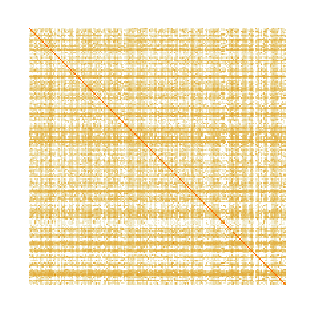

```mathematica
MatrixPlot[WPSMatrix[2020],Frame->False]
```

Number of negative values in the matrix above:

```mathematica
Count[Sign[Flatten[WPSMatrix[2020]]],-1]
```

25

#### International Trade Network (ITN)

Display a graph of the international trade network for a given year. This shows each country’s primary trading partner.

```mathematica
ITNGraph[year_]:=Block[{T},
T=Transpose[Map[OneHotEncodeMax,Transpose[TradeMatrix[year]]]];
T=Sign[T+Transpose[T]];
AdjacencyGraph[T,VertexLabels->MapIndexed[First[#2]->CountryName[#1]&,Range[193]]]
]
```

International Trade Network, 2020 (with Chinese, American, and German clusters).

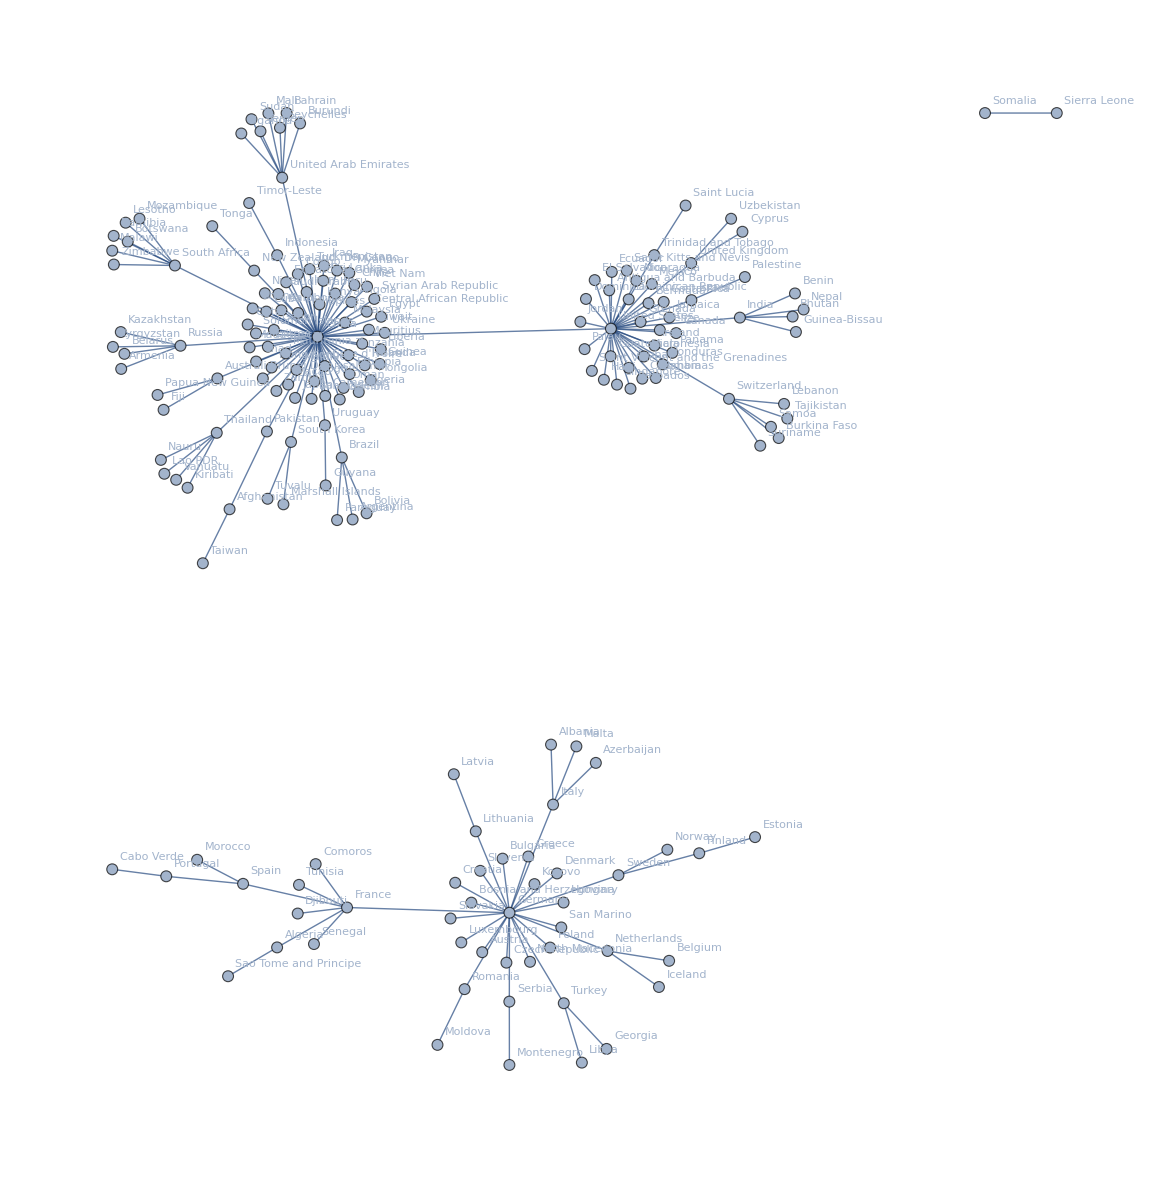

```mathematica
ITNGraph[2020]
```

International Trade Network, 1996 (with American, European, and Chinese clusters).

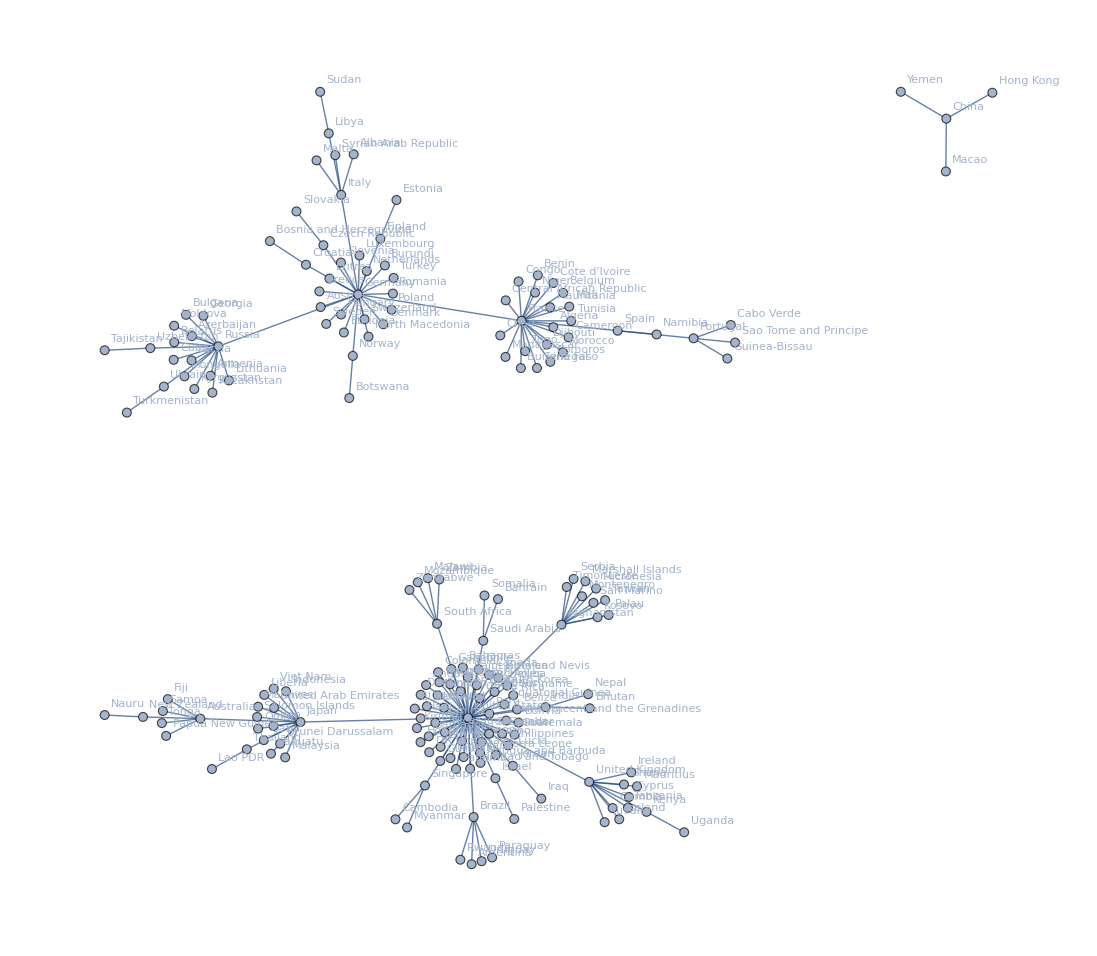

```mathematica
ITNGraph[1996]
```

#### Current trajectory: US and China

```mathematica
sim=NestList[UpdateS[#,Tpos[2020],Tneg[2020],Tzed[2020]]&,WealthVector[2020],25];SizeSeriesSubsetPlot[sim,Map[CountryID,{"United States","China"}],2020,""]
```

-Graphics-

#### Hypothetical ITN: Representative scenario from Swing States

```mathematica
us=Map[CountryID,{"Afghanistan","Algeria","Antigua and Barbuda","Aruba","Bahamas","Bahrain","Barbados","Bermuda","Canada","Costa Rica","Cyprus","Dominica","Dominican Republic","Ecuador","Gabon","Guatemala","Haiti","Iceland","Maldives","Mexico","Micronesia","Panama","Saint Kitts and Nevis","Saint Lucia","Saint Vincent and the Grenadines","Samoa","Seychelles","Singapore","Taiwan","Trinidad and Tobago","Tuvalu","United States"}];
china=Map[CountryID,{"Albania","Angola","Armenia","Australia","Austria","Azerbaijan","Belgium","Bosnia and Herzegovina","Brunei Darussalam","Burkina Faso","Burundi","Cambodia","Cameroon","Central African Republic","China","Colombia","Comoros","Congo","Croatia","Czech Republic","DR Congo","Equatorial Guinea","Georgia","Guinea","Guinea-Bissau","Hong Kong","Hungary","Indonesia","Iraq","Ireland","Jamaica","Kazakhstan","Kiribati","Kosovo","Kyrgyzstan","Lao PDR","Lesotho","Liberia","Mali","Mauritius","Moldova","Myanmar","Namibia","Nauru","Nepal","Netherlands","Niger","North Macedonia","Palestine","Romania","Rwanda","Serbia","Slovakia","Solomon Islands","South Africa","Sri Lanka","Tanzania","Turkmenistan","Uganda","Uruguay","Uzbekistan","Yemen","Zambia","Zimbabwe"}];
T=TradeMatrix[2020];
pct=.1;
allies=us; opps=china;
newT=Fold[ReallocateTrade,T,allies];
allies=china;opps=us;
newT=Fold[ReallocateTrade,newT,allies];
```

Growth of China and U.S. in simulation

```mathematica
sim=NestList[UpdateS[#,NormalizeT[NormalizationVector[2020],newT],Tneg[2020],Tzed[2020]]&,WealthVector[2020],25];SizeSeriesSubsetPlot[sim,Map[CountryID,{"United States","China"}],2020,""]
```

-Graphics-

Total wealth of each coalition

```mathematica
blue=Total[Transpose[sim][[us]]];
red=Total[Transpose[sim][[china]]] ;
ListLinePlot[Map[Transpose[{Range[2020,2020+Length[sim]-1],#}]&,{blue,red}],PlotLabels->{"U.S.-led coalition","China-led coalition"},AxesLabel->{"Year","USD 2020"},PlotRange->All,PlotLabel->"Likely Coalitions"]
```

-Graphics-

#### Hypothetical ITN: Balancing Coalition

```mathematica
us=Map[CountryID,{"United States","Canada","Japan","Germany","South Korea","France","Taiwan","United Kingdom","Spain","Australia"}];
china=Map[CountryID,{"China","Russia","Iran","Pakistan","Indonesia","United Arab Emirates","Nigeria"}];
T=TradeMatrix[2020];
pct=.1;
allies=us; opps=china;
newT=Fold[ReallocateTrade,T,allies];
allies=china;opps=us;
newT=Fold[ReallocateTrade,newT,allies];
```

Growth of China and U.S. in simulation

```mathematica
sim=NestList[UpdateS[#,NormalizeT[NormalizationVector[2020],newT],Tneg[2020],Tzed[2020]]&,WealthVector[2020],25];SizeSeriesSubsetPlot[sim,Map[CountryID,{"United States","China"}],2020,""]
```

Total wealth of each coalition

```mathematica
blue=Total[Transpose[sim][[us]]];
red=Total[Transpose[sim][[china]]] ;
ListLinePlot[Map[Transpose[{Range[2020,2020+Length[sim]-1],#}]&,{blue,red}],PlotLabels->{"U.S.-led coalition","China-led coalition"},AxesLabel->{"Year","USD 2020"},PlotRange->All,PlotLabel->"Balancing Coalition"]
```

-Graphics-